```mathematica
myData[n_]:=ReadList[StringJoin["d:\\Triangle\\Data\\Summ357_UpTo_",ToString[n],".txt"],Number, RecordLists->True ]
```

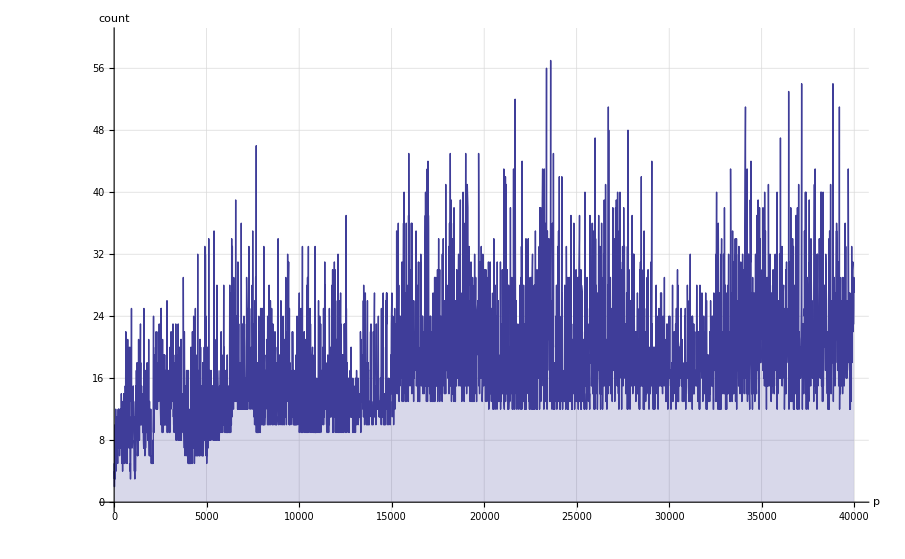

```mathematica
ListPlot[{myData[50]}, Joined->True,  Filling->Axis, PlotRange->{All,{0,60}}, GridLines->Automatic, AxesLabel->{"p","count"}]
```

```mathematica
Select[myData[30], #[[2]]>50&]
```

{{21673,52},{23593,57},{34123,51},{36457,53},{39199,51}}

```mathematica
FullSimplify[InterpolatingPolynomial[Take[myData[40],10],x]]
```

3+((-43+x) (-31+x) (-29+x) (-19+x) (-11+x) (38361505+x (-5944549+x (322197+x (-7439+62 x)))))/49816166400

```mathematica
Plot[3+((-43+x) (-31+x) (-29+x) (-19+x) (-11+x) (38361505+x (-5944549+x (322197+x (-7439+62 x)))))/49816166400, {x,1,40000}]
```

-Graphics-

```mathematica
myPrimes = Table[n[[1]], {n, myData[50]}]
```

{11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541,547,557,563,569,571,577,587,593,599,601,607,613,617,619,631,641,643,647,653,659,661,673,677,683,691,701,709,719,727,733,739,743,751,757,761,769,773,787,797,809,811,821,823,827,829,839,853,857,859,863,877,881,883,887,907,911,919,929,937,941,947,953,967,971,977,983,991,997,1009,1013,1019,1021,1031,1033,1039,1049,1051,1061,1063,1069,1087,1091,1093,1097,1103,1109,1117,1123,1129,1151,1153,1163,1171,1181,1187,1193,1201,1213,1217,1223,1229,1231,1237,1249,1259,1277,1279,1283,1289,1291,1297,1301,1303,1307,1319,1321,1327,1361,1367,1373,1381,1399,1409,1423,1427,1429,1433,1439,1447,1451,1453,1459,1471,1481,1483,1487,1489,1493,1499,1511,1523,1531,1543,1549,1553,1559,1567,1571,1579,1583,1597,1601,1607,1609,1613,1619,1621,1627,1637,1657,1663,1667,1669,1693,1697,1699,1709,1721,1723,1733,1741,1747,1753,1759,1777,1783,1787,1789,1801,1811,1823,1831,1847,1861,1867,1871,1873,1877,1879,1889,1901,1907,1913,1931,1933,1949,1951,1973,1979,1987,1993,1997,1999,2003,2011,2017,2027,2029,2039,2053,2063,2069,2081,2083,2087,2089,2099,2111,2113,2129,2131,2137,2141,2143,2153,2161,2179,2203,2207,2213,2221,2237,2239,2243,2251,2267,2269,2273,2281,2287,2293,2297,2309,2311,2333,2339,2341,2347,2351,2357,2371,2377,2381,2383,2389,2393,2399,2411,2417,2423,2437,2441,2447,2459,2467,2473,2477,2503,2521,2531,2539,2543,2549,2551,2557,2579,2591,2593,2609,2617,2621,2633,2647,2657,2659,2663,2671,2677,2683,2687,2689,2693,2699,2707,2711,2713,2719,2729,2731,2741,2749,2753,2767,2777,2789,2791,2797,2801,2803,2819,2833,2837,2843,2851,2857,2861,2879,2887,2897,2903,2909,2917,2927,2939,2953,2957,2963,2969,2971,2999,3001,3011,3019,3023,3037,3041,3049,3061,3067,3079,3083,3089,3109,3119,3121,3137,3163,3167,3169,3181,3187,3191,3203,3209,3217,3221,3229,3251,3253,3257,3259,3271,3299,3301,3307,3313,3319,3323,3329,3331,3343,3347,3359,3361,3371,3373,3389,3391,3407,3413,3433,3449,3457,3461,3463,3467,3469,3491,3499,3511,3517,3527,3529,3533,3539,3541,3547,3557,3559,3571,3581,3583,3593,3607,3613,3617,3623,3631,3637,3643,3659,3671,3673,3677,3691,3697,3701,3709,3719,3727,3733,3739,3761,3767,3769,3779,3793,3797,3803,3821,3823,3833,3847,3851,3853,3863,3877,3881,3889,3907,3911,3917,3919,3923,3929,3931,3943,3947,3967,3989,4001,4003,4007,4013,4019,4021,4027,4049,4051,4057,4073,4079,4091,4093,4099,4111,4127,4129,4133,4139,4153,4157,4159,4177,4201,4211,4217,4219,4229,4231,4241,4243,4253,4259,4261,4271,4273,4283,4289,4297,4327,4337,4339,4349,4357,4363,4373,4391,4397,4409,4421,4423,4441,4447,4451,4457,4463,4481,4483,4493,4507,4513,4517,4519,4523,4547,4549,4561,4567,4583,4591,4597,4603,4621,4637,4639,4643,4649,4651,4657,4663,4673,4679,4691,4703,4721,4723,4729,4733,4751,4759,4783,4787,4789,4793,4799,4801,4813,4817,4831,4861,4871,4877,4889,4903,4909,4919,4931,4933,4937,4943,4951,4957,4967,4969,4973,4987,4993,4999,5003,5009,5011,5021,5023,5039,5051,5059,5077,5081,5087,5099,5101,5107,5113,5119,5147,5153,5167,5171,5179,5189,5197,5209,5227,5231,5233,5237,5261,5273,5279,5281,5297,5303,5309,5323,5333,5347,5351,5381,5387,5393,5399,5407,5413,5417,5419,5431,5437,5441,5443,5449,5471,5477,5479,5483,5501,5503,5507,5519,5521,5527,5531,5557,5563,5569,5573,5581,5591,5623,5639,5641,5647,5651,5653,5657,5659,5669,5683,5689,5693,5701,5711,5717,5737,5741,5743,5749,5779,5783,5791,5801,5807,5813,5821,5827,5839,5843,5849,5851,5857,5861,5867,5869,5879,5881,5897,5903,5923,5927,5939,5953,5981,5987,6007,6011,6029,6037,6043,6047,6053,6067,6073,6079,6089,6091,6101,6113,6121,6131,6133,6143,6151,6163,6173,6197,6199,6203,6211,6217,6221,6229,6247,6257,6263,6269,6271,6277,6287,6299,6301,6311,6317,6323,6329,6337,6343,6353,6359,6361,6367,6373,6379,6389,6397,6421,6427,6449,6451,6469,6473,6481,6491,6521,6529,6547,6551,6553,6563,6569,6571,6577,6581,6599,6607,6619,6637,6653,6659,6661,6673,6679,6689,6691,6701,6703,6709,6719,6733,6737,6761,6763,6779,6781,6791,6793,6803,6823,6827,6829,6833,6841,6857,6863,6869,6871,6883,6899,6907,6911,6917,6947,6949,6959,6961,6967,6971,6977,6983,6991,6997,7001,7013,7019,7027,7039,7043,7057,7069,7079,7103,7109,7121,7127,7129,7151,7159,7177,7187,7193,7207,7211,7213,7219,7229,7237,7243,7247,7253,7283,7297,7307,7309,7321,7331,7333,7349,7351,7369,7393,7411,7417,7433,7451,7457,7459,7477,7481,7487,7489,7499,7507,7517,7523,7529,7537,7541,7547,7549,7559,7561,7573,7577,7583,7589,7591,7603,7607,7621,7639,7643,7649,7669,7673,7681,7687,7691,7699,7703,7717,7723,7727,7741,7753,7757,7759,7789,7793,7817,7823,7829,7841,7853,7867,7873,7877,7879,7883,7901,7907,7919,7927,7933,7937,7949,7951,7963,7993,8009,8011,8017,8039,8053,8059,8069,8081,8087,8089,8093,8101,8111,8117,8123,8147,8161,8167,8171,8179,8191,8209,8219,8221,8231,8233,8237,8243,8263,8269,8273,8287,8291,8293,8297,8311,8317,8329,8353,8363,8369,8377,8387,8389,8419,8423,8429,8431,8443,8447,8461,8467,8501,8513,8521,8527,8537,8539,8543,8563,8573,8581,8597,8599,8609,8623,8627,8629,8641,8647,8663,8669,8677,8681,8689,8693,8699,8707,8713,8719,8731,8737,8741,8747,8753,8761,8779,8783,8803,8807,8819,8821,8831,8837,8839,8849,8861,8863,8867,8887,8893,8923,8929,8933,8941,8951,8963,8969,8971,8999,9001,9007,9011,9013,9029,9041,9043,9049,9059,9067,9091,9103,9109,9127,9133,9137,9151,9157,9161,9173,9181,9187,9199,9203,9209,9221,9227,9239,9241,9257,9277,9281,9283,9293,9311,9319,9323,9337,9341,9343,9349,9371,9377,9391,9397,9403,9413,9419,9421,9431,9433,9437,9439,9461,9463,9467,9473,9479,9491,9497,9511,9521,9533,9539,9547,9551,9587,9601,9613,9619,9623,9629,9631,9643,9649,9661,9677,9679,9689,9697,9719,9721,9733,9739,9743,9749,9767,9769,9781,9787,9791,9803,9811,9817,9829,9833,9839,9851,9857,9859,9871,9883,9887,9901,9907,9923,9929,9931,9941,9949,9967,9973,10007,10009,10037,10039,10061,10067,10069,10079,10091,10093,10099,10103,10111,10133,10139,10141,10151,10159,10163,10169,10177,10181,10193,10211,10223,10243,10247,10253,10259,10267,10271,10273,10289,10301,10303,10313,10321,10331,10333,10337,10343,10357,10369,10391,10399,10427,10429,10433,10453,10457,10459,10463,10477,10487,10499,10501,10513,10529,10531,10559,10567,10589,10597,10601,10607,10613,10627,10631,10639,10651,10657,10663,10667,10687,10691,10709,10711,10723,10729,10733,10739,10753,10771,10781,10789,10799,10831,10837,10847,10853,10859,10861,10867,10883,10889,10891,10903,10909,10937,10939,10949,10957,10973,10979,10987,10993,11003,11027,11047,11057,11059,11069,11071,11083,11087,11093,11113,11117,11119,11131,11149,11159,11161,11171,11173,11177,11197,11213,11239,11243,11251,11257,11261,11273,11279,11287,11299,11311,11317,11321,11329,11351,11353,11369,11383,11393,11399,11411,11423,11437,11443,11447,11467,11471,11483,11489,11491,11497,11503,11519,11527,11549,11551,11579,11587,11593,11597,11617,11621,11633,11657,11677,11681,11689,11699,11701,11717,11719,11731,11743,11777,11779,11783,11789,11801,11807,11813,11821,11827,11831,11833,11839,11863,11867,11887,11897,11903,11909,11923,11927,11933,11939,11941,11953,11959,11969,11971,11981,11987,12007,12011,12037,12041,12043,12049,12071,12073,12097,12101,12107,12109,12113,12119,12143,12149,12157,12161,12163,12197,12203,12211,12227,12239,12241,12251,12253,12263,12269,12277,12281,12289,12301,12323,12329,12343,12347,12373,12377,12379,12391,12401,12409,12413,12421,12433,12437,12451,12457,12473,12479,12487,12491,12497,12503,12511,12517,12527,12539,12541,12547,12553,12569,12577,12583,12589,12601,12611,12613,12619,12637,12641,12647,12653,12659,12671,12689,12697,12703,12713,12721,12739,12743,12757,12763,12781,12791,12799,12809,12821,12823,12829,12841,12853,12889,12893,12899,12907,12911,12917,12919,12923,12941,12953,12959,12967,12973,12979,12983,13001,13003,13007,13009,13033,13037,13043,13049,13063,13093,13099,13103,13109,13121,13127,13147,13151,13159,13163,13171,13177,13183,13187,13217,13219,13229,13241,13249,13259,13267,13291,13297,13309,13313,13327,13331,13337,13339,13367,13381,13397,13399,13411,13417,13421,13441,13451,13457,13463,13469,13477,13487,13499,13513,13523,13537,13553,13567,13577,13591,13597,13613,13619,13627,13633,13649,13669,13679,13681,13687,13691,13693,13697,13709,13711,13721,13723,13729,13751,13757,13759,13763,13781,13789,13799,13807,13829,13831,13841,13859,13873,13877,13879,13883,13901,13903,13907,13913,13921,13931,13933,13963,13967,13997,13999,14009,14011,14029,14033,14051,14057,14071,14081,14083,14087,14107,14143,14149,14153,14159,14173,14177,14197,14207,14221,14243,14249,14251,14281,14293,14303,14321,14323,14327,14341,14347,14369,14387,14389,14401,14407,14411,14419,14423,14431,14437,14447,14449,14461,14479,14489,14503,14519,14533,14537,14543,14549,14551,14557,14561,14563,14591,14593,14621,14627,14629,14633,14639,14653,14657,14669,14683,14699,14713,14717,14723,14731,14737,14741,14747,14753,14759,14767,14771,14779,14783,14797,14813,14821,14827,14831,14843,14851,14867,14869,14879,14887,14891,14897,14923,14929,14939,14947,14951,14957,14969,14983,15013,15017,15031,15053,15061,15073,15077,15083,15091,15101,15107,15121,15131,15137,15139,15149,15161,15173,15187,15193,15199,15217,15227,15233,15241,15259,15263,15269,15271,15277,15287,15289,15299,15307,15313,15319,15329,15331,15349,15359,15361,15373,15377,15383,15391,15401,15413,15427,15439,15443,15451,15461,15467,15473,15493,15497,15511,15527,15541,15551,15559,15569,15581,15583,15601,15607,15619,15629,15641,15643,15647,15649,15661,15667,15671,15679,15683,15727,15731,15733,15737,15739,15749,15761,15767,15773,15787,15791,15797,15803,15809,15817,15823,15859,15877,15881,15887,15889,15901,15907,15913,15919,15923,15937,15959,15971,15973,15991,16001,16007,16033,16057,16061,16063,16067,16069,16073,16087,16091,16097,16103,16111,16127,16139,16141,16183,16187,16189,16193,16217,16223,16229,16231,16249,16253,16267,16273,16301,16319,16333,16339,16349,16361,16363,16369,16381,16411,16417,16421,16427,16433,16447,16451,16453,16477,16481,16487,16493,16519,16529,16547,16553,16561,16567,16573,16603,16607,16619,16631,16633,16649,16651,16657,16661,16673,16691,16693,16699,16703,16729,16741,16747,16759,16763,16787,16811,16823,16829,16831,16843,16871,16879,16883,16889,16901,16903,16921,16927,16931,16937,16943,16963,16979,16981,16987,16993,17011,17021,17027,17029,17033,17041,17047,17053,17077,17093,17099,17107,17117,17123,17137,17159,17167,17183,17189,17191,17203,17207,17209,17231,17239,17257,17291,17293,17299,17317,17321,17327,17333,17341,17351,17359,17377,17383,17387,17389,17393,17401,17417,17419,17431,17443,17449,17467,17471,17477,17483,17489,17491,17497,17509,17519,17539,17551,17569,17573,17579,17581,17597,17599,17609,17623,17627,17657,17659,17669,17681,17683,17707,17713,17729,17737,17747,17749,17761,17783,17789,17791,17807,17827,17837,17839,17851,17863,17881,17891,17903,17909,17911,17921,17923,17929,17939,17957,17959,17971,17977,17981,17987,17989,18013,18041,18043,18047,18049,18059,18061,18077,18089,18097,18119,18121,18127,18131,18133,18143,18149,18169,18181,18191,18199,18211,18217,18223,18229,18233,18251,18253,18257,18269,18287,18289,18301,18307,18311,18313,18329,18341,18353,18367,18371,18379,18397,18401,18413,18427,18433,18439,18443,18451,18457,18461,18481,18493,18503,18517,18521,18523,18539,18541,18553,18583,18587,18593,18617,18637,18661,18671,18679,18691,18701,18713,18719,18731,18743,18749,18757,18773,18787,18793,18797,18803,18839,18859,18869,18899,18911,18913,18917,18919,18947,18959,18973,18979,19001,19009,19013,19031,19037,19051,19069,19073,19079,19081,19087,19121,19139,19141,19157,19163,19181,19183,19207,19211,19213,19219,19231,19237,19249,19259,19267,19273,19289,19301,19309,19319,19333,19373,19379,19381,19387,19391,19403,19417,19421,19423,19427,19429,19433,19441,19447,19457,19463,19469,19471,19477,19483,19489,19501,19507,19531,19541,19543,19553,19559,19571,19577,19583,19597,19603,19609,19661,19681,19687,19697,19699,19709,19717,19727,19739,19751,19753,19759,19763,19777,19793,19801,19813,19819,19841,19843,19853,19861,19867,19889,19891,19913,19919,19927,19937,19949,19961,19963,19973,19979,19991,19993,19997,20011,20021,20023,20029,20047,20051,20063,20071,20089,20101,20107,20113,20117,20123,20129,20143,20147,20149,20161,20173,20177,20183,20201,20219,20231,20233,20249,20261,20269,20287,20297,20323,20327,20333,20341,20347,20353,20357,20359,20369,20389,20393,20399,20407,20411,20431,20441,20443,20477,20479,20483,20507,20509,20521,20533,20543,20549,20551,20563,20593,20599,20611,20627,20639,20641,20663,20681,20693,20707,20717,20719,20731,20743,20747,20749,20753,20759,20771,20773,20789,20807,20809,20849,20857,20873,20879,20887,20897,20899,20903,20921,20929,20939,20947,20959,20963,20981,20983,21001,21011,21013,21017,21019,21023,21031,21059,21061,21067,21089,21101,21107,21121,21139,21143,21149,21157,21163,21169,21179,21187,21191,21193,21211,21221,21227,21247,21269,21277,21283,21313,21317,21319,21323,21341,21347,21377,21379,21383,21391,21397,21401,21407,21419,21433,21467,21481,21487,21491,21493,21499,21503,21517,21521,21523,21529,21557,21559,21563,21569,21577,21587,21589,21599,21601,21611,21613,21617,21647,21649,21661,21673,21683,21701,21713,21727,21737,21739,21751,21757,21767,21773,21787,21799,21803,21817,21821,21839,21841,21851,21859,21863,21871,21881,21893,21911,21929,21937,21943,21961,21977,21991,21997,22003,22013,22027,22031,22037,22039,22051,22063,22067,22073,22079,22091,22093,22109,22111,22123,22129,22133,22147,22153,22157,22159,22171,22189,22193,22229,22247,22259,22271,22273,22277,22279,22283,22291,22303,22307,22343,22349,22367,22369,22381,22391,22397,22409,22433,22441,22447,22453,22469,22481,22483,22501,22511,22531,22541,22543,22549,22567,22571,22573,22613,22619,22621,22637,22639,22643,22651,22669,22679,22691,22697,22699,22709,22717,22721,22727,22739,22741,22751,22769,22777,22783,22787,22807,22811,22817,22853,22859,22861,22871,22877,22901,22907,22921,22937,22943,22961,22963,22973,22993,23003,23011,23017,23021,23027,23029,23039,23041,23053,23057,23059,23063,23071,23081,23087,23099,23117,23131,23143,23159,23167,23173,23189,23197,23201,23203,23209,23227,23251,23269,23279,23291,23293,23297,23311,23321,23327,23333,23339,23357,23369,23371,23399,23417,23431,23447,23459,23473,23497,23509,23531,23537,23539,23549,23557,23561,23563,23567,23581,23593,23599,23603,23609,23623,23627,23629,23633,23663,23669,23671,23677,23687,23689,23719,23741,23743,23747,23753,23761,23767,23773,23789,23801,23813,23819,23827,23831,23833,23857,23869,23873,23879,23887,23893,23899,23909,23911,23917,23929,23957,23971,23977,23981,23993,24001,24007,24019,24023,24029,24043,24049,24061,24071,24077,24083,24091,24097,24103,24107,24109,24113,24121,24133,24137,24151,24169,24179,24181,24197,24203,24223,24229,24239,24247,24251,24281,24317,24329,24337,24359,24371,24373,24379,24391,24407,24413,24419,24421,24439,24443,24469,24473,24481,24499,24509,24517,24527,24533,24547,24551,24571,24593,24611,24623,24631,24659,24671,24677,24683,24691,24697,24709,24733,24749,24763,24767,24781,24793,24799,24809,24821,24841,24847,24851,24859,24877,24889,24907,24917,24919,24923,24943,24953,24967,24971,24977,24979,24989,25013,25031,25033,25037,25057,25073,25087,25097,25111,25117,25121,25127,25147,25153,25163,25169,25171,25183,25189,25219,25229,25237,25243,25247,25253,25261,25301,25303,25307,25309,25321,25339,25343,25349,25357,25367,25373,25391,25409,25411,25423,25439,25447,25453,25457,25463,25469,25471,25523,25537,25541,25561,25577,25579,25583,25589,25601,25603,25609,25621,25633,25639,25643,25657,25667,25673,25679,25693,25703,25717,25733,25741,25747,25759,25763,25771,25793,25799,25801,25819,25841,25847,25849,25867,25873,25889,25903,25913,25919,25931,25933,25939,25943,25951,25969,25981,25997,25999,26003,26017,26021,26029,26041,26053,26083,26099,26107,26111,26113,26119,26141,26153,26161,26171,26177,26183,26189,26203,26209,26227,26237,26249,26251,26261,26263,26267,26293,26297,26309,26317,26321,26339,26347,26357,26371,26387,26393,26399,26407,26417,26423,26431,26437,26449,26459,26479,26489,26497,26501,26513,26539,26557,26561,26573,26591,26597,26627,26633,26641,26647,26669,26681,26683,26687,26693,26699,26701,26711,26713,26717,26723,26729,26731,26737,26759,26777,26783,26801,26813,26821,26833,26839,26849,26861,26863,26879,26881,26891,26893,26903,26921,26927,26947,26951,26953,26959,26981,26987,26993,27011,27017,27031,27043,27059,27061,27067,27073,27077,27091,27103,27107,27109,27127,27143,27179,27191,27197,27211,27239,27241,27253,27259,27271,27277,27281,27283,27299,27329,27337,27361,27367,27397,27407,27409,27427,27431,27437,27449,27457,27479,27481,27487,27509,27527,27529,27539,27541,27551,27581,27583,27611,27617,27631,27647,27653,27673,27689,27691,27697,27701,27733,27737,27739,27743,27749,27751,27763,27767,27773,27779,27791,27793,27799,27803,27809,27817,27823,27827,27847,27851,27883,27893,27901,27917,27919,27941,27943,27947,27953,27961,27967,27983,27997,28001,28019,28027,28031,28051,28057,28069,28081,28087,28097,28099,28109,28111,28123,28151,28163,28181,28183,28201,28211,28219,28229,28277,28279,28283,28289,28297,28307,28309,28319,28349,28351,28387,28393,28403,28409,28411,28429,28433,28439,28447,28463,28477,28493,28499,28513,28517,28537,28541,28547,28549,28559,28571,28573,28579,28591,28597,28603,28607,28619,28621,28627,28631,28643,28649,28657,28661,28663,28669,28687,28697,28703,28711,28723,28729,28751,28753,28759,28771,28789,28793,28807,28813,28817,28837,28843,28859,28867,28871,28879,28901,28909,28921,28927,28933,28949,28961,28979,29009,29017,29021,29023,29027,29033,29059,29063,29077,29101,29123,29129,29131,29137,29147,29153,29167,29173,29179,29191,29201,29207,29209,29221,29231,29243,29251,29269,29287,29297,29303,29311,29327,29333,29339,29347,29363,29383,29387,29389,29399,29401,29411,29423,29429,29437,29443,29453,29473,29483,29501,29527,29531,29537,29567,29569,29573,29581,29587,29599,29611,29629,29633,29641,29663,29669,29671,29683,29717,29723,29741,29753,29759,29761,29789,29803,29819,29833,29837,29851,29863,29867,29873,29879,29881,29917,29921,29927,29947,29959,29983,29989,30011,30013,30029,30047,30059,30071,30089,30091,30097,30103,30109,30113,30119,30133,30137,30139,30161,30169,30181,30187,30197,30203,30211,30223,30241,30253,30259,30269,30271,30293,30307,30313,30319,30323,30341,30347,30367,30389,30391,30403,30427,30431,30449,30467,30469,30491,30493,30497,30509,30517,30529,30539,30553,30557,30559,30577,30593,30631,30637,30643,30649,30661,30671,30677,30689,30697,30703,30707,30713,30727,30757,30763,30773,30781,30803,30809,30817,30829,30839,30841,30851,30853,30859,30869,30871,30881,30893,30911,30931,30937,30941,30949,30971,30977,30983,31013,31019,31033,31039,31051,31063,31069,31079,31081,31091,31121,31123,31139,31147,31151,31153,31159,31177,31181,31183,31189,31193,31219,31223,31231,31237,31247,31249,31253,31259,31267,31271,31277,31307,31319,31321,31327,31333,31337,31357,31379,31387,31391,31393,31397,31469,31477,31481,31489,31511,31513,31517,31531,31541,31543,31547,31567,31573,31583,31601,31607,31627,31643,31649,31657,31663,31667,31687,31699,31721,31723,31727,31729,31741,31751,31769,31771,31793,31799,31817,31847,31849,31859,31873,31883,31891,31907,31957,31963,31973,31981,31991,32003,32009,32027,32029,32051,32057,32059,32063,32069,32077,32083,32089,32099,32117,32119,32141,32143,32159,32173,32183,32189,32191,32203,32213,32233,32237,32251,32257,32261,32297,32299,32303,32309,32321,32323,32327,32341,32353,32359,32363,32369,32371,32377,32381,32401,32411,32413,32423,32429,32441,32443,32467,32479,32491,32497,32503,32507,32531,32533,32537,32561,32563,32569,32573,32579,32587,32603,32609,32611,32621,32633,32647,32653,32687,32693,32707,32713,32717,32719,32749,32771,32779,32783,32789,32797,32801,32803,32831,32833,32839,32843,32869,32887,32909,32911,32917,32933,32939,32941,32957,32969,32971,32983,32987,32993,32999,33013,33023,33029,33037,33049,33053,33071,33073,33083,33091,33107,33113,33119,33149,33151,33161,33179,33181,33191,33199,33203,33211,33223,33247,33287,33289,33301,33311,33317,33329,33331,33343,33347,33349,33353,33359,33377,33391,33403,33409,33413,33427,33457,33461,33469,33479,33487,33493,33503,33521,33529,33533,33547,33563,33569,33577,33581,33587,33589,33599,33601,33613,33617,33619,33623,33629,33637,33641,33647,33679,33703,33713,33721,33739,33749,33751,33757,33767,33769,33773,33791,33797,33809,33811,33827,33829,33851,33857,33863,33871,33889,33893,33911,33923,33931,33937,33941,33961,33967,33997,34019,34031,34033,34039,34057,34061,34123,34127,34129,34141,34147,34157,34159,34171,34183,34211,34213,34217,34231,34253,34259,34261,34267,34273,34283,34297,34301,34303,34313,34319,34327,34337,34351,34361,34367,34369,34381,34403,34421,34429,34439,34457,34469,34471,34483,34487,34499,34501,34511,34513,34519,34537,34543,34549,34583,34589,34591,34603,34607,34613,34631,34649,34651,34667,34673,34679,34687,34693,34703,34721,34729,34739,34747,34757,34759,34763,34781,34807,34819,34841,34843,34847,34849,34871,34877,34883,34897,34913,34919,34939,34949,34961,34963,34981,35023,35027,35051,35053,35059,35069,35081,35083,35089,35099,35107,35111,35117,35129,35141,35149,35153,35159,35171,35201,35221,35227,35251,35257,35267,35279,35281,35291,35311,35317,35323,35327,35339,35353,35363,35381,35393,35401,35407,35419,35423,35437,35447,35449,35461,35491,35507,35509,35521,35527,35531,35533,35537,35543,35569,35573,35591,35593,35597,35603,35617,35671,35677,35729,35731,35747,35753,35759,35771,35797,35801,35803,35809,35831,35837,35839,35851,35863,35869,35879,35897,35899,35911,35923,35933,35951,35963,35969,35977,35983,35993,35999,36007,36011,36013,36017,36037,36061,36067,36073,36083,36097,36107,36109,36131,36137,36151,36161,36187,36191,36209,36217,36229,36241,36251,36263,36269,36277,36293,36299,36307,36313,36319,36341,36343,36353,36373,36383,36389,36433,36451,36457,36467,36469,36473,36479,36493,36497,36523,36527,36529,36541,36551,36559,36563,36571,36583,36587,36599,36607,36629,36637,36643,36653,36671,36677,36683,36691,36697,36709,36713,36721,36739,36749,36761,36767,36779,36781,36787,36791,36793,36809,36821,36833,36847,36857,36871,36877,36887,36899,36901,36913,36919,36923,36929,36931,36943,36947,36973,36979,36997,37003,37013,37019,37021,37039,37049,37057,37061,37087,37097,37117,37123,37139,37159,37171,37181,37189,37199,37201,37217,37223,37243,37253,37273,37277,37307,37309,37313,37321,37337,37339,37357,37361,37363,37369,37379,37397,37409,37423,37441,37447,37463,37483,37489,37493,37501,37507,37511,37517,37529,37537,37547,37549,37561,37567,37571,37573,37579,37589,37591,37607,37619,37633,37643,37649,37657,37663,37691,37693,37699,37717,37747,37781,37783,37799,37811,37813,37831,37847,37853,37861,37871,37879,37889,37897,37907,37951,37957,37963,37967,37987,37991,37993,37997,38011,38039,38047,38053,38069,38083,38113,38119,38149,38153,38167,38177,38183,38189,38197,38201,38219,38231,38237,38239,38261,38273,38281,38287,38299,38303,38317,38321,38327,38329,38333,38351,38371,38377,38393,38431,38447,38449,38453,38459,38461,38501,38543,38557,38561,38567,38569,38593,38603,38609,38611,38629,38639,38651,38653,38669,38671,38677,38693,38699,38707,38711,38713,38723,38729,38737,38747,38749,38767,38783,38791,38803,38821,38833,38839,38851,38861,38867,38873,38891,38903,38917,38921,38923,38933,38953,38959,38971,38977,38993,39019,39023,39041,39043,39047,39079,39089,39097,39103,39107,39113,39119,39133,39139,39157,39161,39163,39181,39191,39199,39209,39217,39227,39229,39233,39239,39241,39251,39293,39301,39313,39317,39323,39341,39343,39359,39367,39371,39373,39383,39397,39409,39419,39439,39443,39451,39461,39499,39503,39509,39511,39521,39541,39551,39563,39569,39581,39607,39619,39623,39631,39659,39667,39671,39679,39703,39709,39719,39727,39733,39749,39761,39769,39779,39791,39799,39821,39827,39829,39839,39841,39847,39857,39863,39869,39877,39883,39887,39901,39929,39937,39953,39971,39979,39983,39989}

```mathematica
myValues = Accumulate[Table[n[[2]], {n, myData[50]}]]
```

{3,8,10,13,17,20,23,29,36,39,47,57,62,69,74,80,87,91,103,107,112,119,124,131,136,141,148,155,164,173,182,193,201,207,215,224,232,239,244,250,261,268,279,290,302,312,320,331,343,351,359,368,376,383,390,398,406,412,421,433,445,455,466,477,487,497,507,516,523,535,542,550,564,574,582,587,593,598,605,614,624,635,643,647,656,663,675,681,694,706,718,730,743,757,769,776,781,786,793,802,811,821,833,845,855,870,884,896,909,922,944,951,970,977,982,990,1005,1014,1022,1034,1040,1045,1058,1076,1087,1108,1121,1133,1145,1155,1165,1173,1181,1191,1198,1205,1219,1239,1253,1262,1270,1281,1291,1297,1302,1306,1311,1314,1317,1320,1330,1339,1359,1372,1397,1410,1421,1429,1436,1443,1454,1462,1471,1485,1496,1508,1520,1530,1544,1559,1572,1583,1596,1606,1617,1625,1632,1639,1644,1648,1656,1660,1663,1669,1679,1690,1694,1702,1711,1726,1735,1744,1761,1770,1781,1789,1798,1809,1827,1835,1841,1848,1854,1868,1878,1885,1894,1904,1912,1920,1935,1956,1964,1979,1987,1998,2008,2019,2032,2055,2067,2083,2101,2111,2123,2133,2145,2155,2165,2178,2193,2204,2216,2227,2238,2251,2265,2278,2287,2296,2305,2315,2324,2333,2342,2350,2357,2377,2384,2409,2416,2423,2432,2445,2452,2459,2465,2471,2478,2495,2502,2509,2518,2530,2542,2551,2561,2570,2582,2595,2604,2622,2632,2645,2658,2668,2676,2686,2694,2705,2726,2736,2746,2754,2762,2770,2776,2788,2801,2807,2814,2820,2826,2832,2844,2850,2856,2862,2868,2873,2878,2884,2890,2896,2902,2908,2914,2919,2925,2930,2935,2942,2947,2955,2962,2986,2995,3006,3018,3027,3038,3054,3066,3079,3098,3113,3126,3141,3161,3178,3193,3206,3228,3240,3254,3268,3280,3297,3309,3327,3343,3355,3368,3382,3397,3411,3427,3440,3454,3476,3495,3511,3527,3540,3559,3574,3597,3614,3630,3644,3660,3677,3694,3706,3716,3736,3761,3771,3796,3810,3821,3841,3850,3859,3868,3889,3903,3912,3922,3933,3944,3955,3970,3982,3993,4004,4023,4040,4052,4062,4080,4099,4109,4126,4145,4155,4167,4177,4187,4197,4208,4225,4237,4253,4263,4273,4284,4294,4304,4314,4340,4349,4358,4369,4382,4391,4403,4414,4427,4444,4457,4467,4479,4489,4506,4517,4526,4535,4544,4564,4575,4595,4614,4626,4638,4660,4681,4697,4710,4730,4745,4762,4778,4800,4813,4836,4850,4866,4877,4889,4899,4912,4922,4932,4941,4954,4963,4973,4991,5001,5020,5034,5045,5056,5065,5088,5096,5108,5123,5133,5143,5154,5170,5178,5191,5202,5221,5235,5250,5260,5283,5295,5303,5320,5328,5338,5353,5366,5377,5397,5412,5420,5429,5447,5455,5464,5473,5481,5493,5501,5522,5539,5560,5568,5577,5591,5602,5613,5627,5638,5649,5660,5672,5683,5692,5701,5710,5739,5750,5759,5769,5778,5785,5807,5825,5837,5851,5857,5865,5876,5886,5899,5910,5925,5940,5950,5958,5975,5985,5995,6001,6007,6015,6021,6038,6044,6050,6055,6060,6077,6082,6087,6092,6104,6109,6114,6119,6124,6129,6134,6139,6144,6149,6160,6167,6179,6199,6204,6209,6216,6226,6238,6253,6271,6276,6298,6306,6314,6335,6342,6351,6358,6368,6381,6392,6416,6433,6440,6445,6452,6474,6490,6500,6525,6531,6549,6556,6575,6585,6591,6597,6604,6611,6621,6627,6633,6646,6654,6686,6693,6699,6710,6719,6727,6738,6755,6761,6769,6775,6786,6807,6813,6819,6829,6850,6858,6870,6890,6902,6910,6920,6935,6943,6950,6956,6967,6976,6982,7000,7006,7012,7018,7029,7044,7050,7058,7066,7086,7097,7105,7138,7171,7181,7189,7221,7230,7239,7246,7256,7280,7286,7300,7309,7318,7327,7332,7339,7345,7355,7362,7381,7401,7420,7429,7442,7449,7458,7466,7477,7511,7519,7531,7545,7562,7570,7580,7589,7604,7613,7625,7633,7644,7661,7672,7686,7701,7712,7721,7731,7746,7761,7772,7780,7793,7804,7815,7823,7858,7873,7891,7911,7919,7927,7938,7948,7969,7979,7988,8000,8012,8020,8029,8048,8063,8071,8079,8093,8103,8131,8141,8153,8166,8174,8191,8204,8213,8222,8232,8241,8253,8261,8273,8282,8290,8299,8308,8323,8333,8343,8358,8375,8384,8393,8403,8425,8439,8453,8465,8477,8486,8505,8519,8536,8546,8558,8568,8580,8589,8603,8613,8623,8633,8643,8671,8688,8708,8721,8730,8739,8756,8766,8775,8785,8795,8804,8814,8831,8842,8851,8860,8871,8880,8899,8908,8917,8926,8935,8946,8961,8971,8980,8989,9003,9015,9024,9033,9042,9070,9083,9092,9108,9135,9147,9158,9167,9176,9189,9199,9214,9225,9235,9249,9283,9297,9327,9338,9355,9375,9408,9426,9447,9476,9488,9500,9527,9547,9561,9575,9589,9602,9631,9645,9664,9688,9727,9743,9759,9772,9791,9804,9828,9849,9864,9877,9893,9905,9919,9939,9970,9985,9997,10015,10030,10053,10072,10084,10099,10115,10127,10139,10153,10168,10186,10201,10213,10227,10244,10259,10271,10289,10325,10337,10351,10365,10381,10393,10416,10430,10445,10457,10471,10485,10497,10517,10530,10547,10566,10590,10602,10622,10644,10667,10687,10700,10712,10726,10741,10755,10771,10783,10801,10830,10855,10874,10886,10904,10924,10937,10949,10966,10990,11012,11037,11053,11086,11099,11114,11128,11153,11176,11190,11202,11215,11230,11245,11265,11283,11298,11314,11326,11354,11370,11387,11405,11440,11456,11472,11485,11502,11523,11535,11549,11563,11582,11605,11616,11630,11643,11655,11667,11677,11696,11722,11735,11748,11765,11794,11804,11814,11860,11869,11882,11892,11901,11916,11932,11941,11950,11968,11977,11986,11995,12004,12028,12037,12051,12072,12089,12103,12125,12135,12156,12171,12180,12193,12218,12237,12261,12284,12294,12319,12330,12340,12355,12367,12392,12402,12412,12422,12438,12448,12471,12504,12514,12536,12547,12560,12570,12580,12591,12608,12619,12634,12646,12662,12677,12696,12714,12729,12742,12763,12780,12795,12808,12828,12838,12860,12884,12903,12917,12927,12937,12949,12960,12988,13003,13019,13043,13053,13067,13077,13088,13114,13132,13147,13161,13186,13197,13211,13223,13233,13245,13256,13266,13289,13308,13319,13330,13342,13358,13368,13381,13397,13408,13419,13438,13454,13465,13487,13497,13511,13525,13544,13564,13574,13590,13606,13624,13634,13645,13655,13666,13678,13693,13711,13726,13738,13762,13777,13792,13826,13842,13852,13862,13873,13888,13899,13918,13930,13941,13952,13962,13974,13985,14002,14018,14044,14056,14067,14078,14097,14107,14122,14133,14149,14159,14183,14195,14213,14228,14239,14250,14260,14271,14283,14293,14313,14334,14349,14360,14375,14388,14407,14436,14447,14463,14485,14495,14512,14526,14540,14553,14569,14586,14608,14640,14658,14672,14696,14711,14725,14754,14785,14806,14831,14846,14864,14881,14891,14916,14926,14940,14958,14970,14987,15004,15021,15032,15042,15054,15070,15082,15094,15105,15116,15138,15151,15173,15184,15195,15206,15216,15233,15243,15258,15275,15286,15296,15307,15317,15327,15338,15348,15360,15372,15382,15397,15416,15433,15443,15453,15469,15484,15494,15505,15529,15541,15554,15569,15579,15595,15610,15621,15632,15646,15673,15682,15693,15702,15714,15728,15740,15750,15770,15785,15810,15821,15831,15840,15851,15860,15876,15890,15899,15912,15945,15954,15967,15985,15996,16015,16034,16052,16071,16081,16090,16112,16126,16138,16151,16167,16178,16194,16215,16225,16234,16248,16265,16274,16285,16296,16324,16333,16362,16371,16395,16405,16431,16444,16477,16487,16497,16510,16519,16543,16564,16589,16606,16619,16629,16652,16661,16672,16682,16692,16704,16721,16734,16743,16756,16775,16794,16814,16824,16834,16853,16862,16872,16881,16891,16906,16917,16926,16937,16946,16956,16989,16998,17007,17018,17027,17037,17046,17056,17065,17081,17091,17104,17117,17132,17141,17153,17166,17192,17204,17222,17231,17242,17251,17264,17282,17306,17316,17339,17349,17361,17378,17401,17410,17419,17429,17446,17456,17467,17482,17493,17507,17518,17531,17541,17561,17572,17587,17612,17622,17639,17652,17663,17680,17711,17732,17760,17772,17786,17799,17817,17830,17842,17853,17863,17874,17890,17901,17910,17919,17934,17953,17966,17975,17990,17999,18014,18024,18035,18060,18075,18095,18106,18118,18135,18149,18164,18175,18186,18198,18226,18243,18255,18270,18291,18321,18331,18340,18366,18378,18390,18409,18419,18428,18448,18461,18492,18503,18527,18552,18574,18604,18631,18650,18666,18677,18703,18714,18723,18742,18763,18775,18793,18802,18815,18827,18843,18870,18902,18913,18922,18938,18949,18965,18974,18990,18999,19011,19032,19058,19073,19091,19118,19136,19159,19168,19178,19191,19205,19223,19240,19249,19268,19282,19300,19319,19328,19347,19358,19367,19382,19400,19416,19427,19437,19460,19477,19488,19511,19532,19541,19554,19574,19585,19601,19620,19635,19672,19690,19712,19737,19754,19763,19781,19798,19808,19819,19832,19843,19854,19865,19875,19890,19901,19917,19926,19936,19945,19959,19973,19986,19997,20014,20028,20040,20051,20062,20082,20093,20107,20118,20129,20142,20154,20163,20179,20189,20201,20214,20225,20234,20247,20259,20274,20285,20296,20307,20320,20331,20340,20351,20364,20375,20386,20395,20411,20421,20434,20445,20462,20472,20483,20495,20506,20517,20531,20543,20554,20565,20581,20591,20602,20615,20626,20640,20651,20663,20675,20687,20700,20715,20737,20753,20762,20783,20796,20814,20827,20841,20860,20873,20888,20901,20915,20930,20942,20954,20980,20991,21019,21036,21049,21067,21077,21094,21107,21134,21154,21171,21183,21196,21207,21217,21227,21239,21256,21274,21286,21312,21322,21332,21342,21356,21368,21386,21398,21410,21420,21430,21441,21454,21464,21477,21488,21500,21517,21534,21556,21568,21580,21592,21615,21628,21640,21651,21664,21676,21686,21696,21706,21717,21729,21739,21751,21773,21784,21798,21815,21838,21865,21876,21888,21902,21915,21927,21937,21952,21964,21987,22004,22017,22029,22042,22055,22069,22081,22105,22118,22130,22143,22154,22167,22179,22190,22202,22216,22232,22248,22263,22275,22288,22299,22312,22322,22347,22360,22377,22389,22406,22417,22429,22442,22454,22481,22492,22512,22522,22532,22544,22557,22568,22578,22590,22600,22614,22627,22637,22650,22662,22677,22703,22716,22742,22769,22792,22816,22843,22856,22868,22880,22890,22902,22914,22928,22941,22953,22964,22977,22993,23003,23013,23026,23038,23052,23065,23077,23090,23106,23116,23129,23140,23152,23171,23185,23208,23235,23249,23273,23286,23310,23321,23344,23357,23369,23392,23402,23417,23429,23446,23460,23473,23498,23510,23525,23545,23559,23574,23588,23607,23630,23645,23661,23696,23724,23740,23759,23777,23796,23821,23835,23859,23877,23898,23923,23959,23982,23996,24021,24049,24064,24077,24091,24108,24127,24142,24162,24186,24210,24229,24248,24264,24284,24302,24318,24340,24371,24384,24401,24430,24444,24466,24479,24506,24542,24561,24575,24596,24617,24633,24673,24689,24708,24735,24752,24765,24778,24793,24808,24826,24839,24862,24878,24914,24929,24955,24968,24982,25000,25017,25037,25065,25085,25104,25117,25142,25179,25196,25241,25265,25281,25311,25327,25342,25370,25390,25420,25441,25460,25496,25519,25547,25566,25586,25600,25636,25652,25673,25692,25711,25730,25747,25760,25783,25809,25826,25842,25862,25880,25902,25924,25942,25959,25978,26013,26039,26054,26074,26091,26110,26134,26155,26168,26194,26209,26237,26255,26286,26304,26324,26339,26358,26377,26390,26403,26420,26440,26471,26489,26509,26541,26556,26571,26591,26609,26628,26652,26672,26688,26704,26728,26742,26760,26775,26791,26813,26829,26843,26858,26873,26899,26932,26969,26984,27024,27043,27070,27083,27103,27126,27143,27162,27205,27237,27261,27274,27305,27349,27364,27386,27423,27458,27473,27495,27511,27533,27552,27574,27589,27603,27627,27643,27656,27680,27699,27716,27729,27750,27765,27787,27807,27823,27836,27849,27864,27878,27905,27918,27942,27962,27988,28001,28030,28043,28067,28096,28113,28129,28144,28160,28189,28209,28227,28251,28275,28294,28309,28336,28351,28373,28400,28430,28454,28470,28483,28498,28515,28535,28569,28587,28608,28623,28646,28667,28697,28710,28729,28746,28767,28791,28807,28822,28841,28855,28876,28892,28905,28937,28957,28973,28992,29010,29044,29070,29086,29102,29117,29136,29150,29176,29193,29212,29233,29259,29277,29291,29332,29354,29371,29388,29409,29433,29453,29479,29507,29526,29544,29560,29587,29611,29628,29655,29678,29705,29738,29752,29778,29802,29838,29865,29883,29902,29917,29962,29987,30010,30025,30059,30098,30116,30152,30165,30183,30204,30218,30232,30247,30261,30295,30311,30331,30345,30364,30389,30402,30431,30469,30488,30503,30526,30547,30562,30575,30590,30603,30624,30640,30666,30690,30705,30720,30750,30766,30785,30807,30835,30851,30867,30887,30913,30945,30960,30977,30993,31009,31029,31059,31098,31113,31139,31161,31188,31207,31225,31242,31255,31279,31294,31320,31360,31375,31393,31429,31460,31473,31491,31506,31534,31557,31572,31617,31642,31666,31682,31718,31732,31755,31785,31813,31840,31881,31919,31934,31949,31980,32008,32041,32064,32090,32105,32122,32148,32164,32177,32192,32207,32221,32246,32277,32292,32305,32329,32345,32374,32387,32403,32416,32432,32453,32466,32489,32508,32526,32540,32562,32578,32597,32610,32628,32656,32674,32695,32727,32750,32769,32783,32807,32836,32861,32876,32897,32915,32930,32943,32956,32972,32996,33022,33041,33063,33096,33141,33178,33193,33220,33248,33262,33279,33305,33325,33356,33372,33390,33420,33436,33456,33489,33514,33534,33562,33578,33591,33606,33622,33654,33671,33687,33714,33730,33745,33769,33796,33820,33843,33864,33889,33919,33939,33966,33982,34002,34015,34045,34075,34097,34124,34139,34157,34176,34191,34204,34233,34258,34277,34300,34327,34348,34367,34398,34420,34432,34446,34467,34495,34510,34541,34571,34587,34614,34628,34650,34665,34683,34705,34718,34733,34755,34780,34794,34808,34833,34848,34875,34887,34907,34919,34936,34970,34984,34998,35020,35036,35055,35067,35095,35115,35133,35148,35172,35185,35204,35216,35247,35264,35278,35295,35308,35324,35337,35356,35382,35395,35411,35430,35443,35460,35475,35490,35506,35537,35549,35572,35586,35599,35613,35627,35641,35657,35671,35694,35715,35745,35759,35777,35800,35817,35838,35854,35884,35897,35940,35953,35965,35982,36011,36039,36052,36077,36119,36132,36157,36181,36195,36213,36254,36273,36298,36316,36330,36360,36380,36392,36406,36421,36449,36477,36489,36503,36521,36541,36556,36569,36582,36600,36614,36630,36668,36687,36703,36724,36742,36771,36786,36805,36819,36842,36868,36880,36900,36922,36947,36959,36973,36993,37036,37068,37091,37108,37139,37153,37173,37205,37217,37247,37299,37337,37352,37373,37395,37421,37435,37451,37463,37475,37487,37501,37515,37533,37547,37570,37586,37602,37620,37634,37646,37658,37678,37695,37709,37737,37753,37770,37782,37794,37812,37841,37858,37891,37914,37943,37962,37974,38018,38033,38059,38083,38099,38121,38136,38150,38164,38187,38208,38236,38251,38274,38287,38303,38317,38329,38346,38358,38382,38416,38434,38446,38467,38486,38508,38528,38544,38558,38573,38598,38620,38651,38685,38701,38724,38741,38754,38769,38781,38807,38823,38835,38864,38879,38900,38914,38943,38964,38977,38989,39003,39028,39060,39072,39088,39104,39126,39151,39168,39181,39193,39208,39225,39245,39273,39288,39300,39315,39327,39355,39377,39412,39442,39463,39492,39505,39521,39543,39555,39585,39597,39615,39635,39651,39671,39687,39705,39722,39739,39757,39790,39802,39840,39865,39884,39898,39913,39947,39962,39978,40002,40021,40059,40072,40091,40111,40126,40141,40169,40192,40231,40274,40299,40320,40339,40354,40375,40409,40435,40447,40490,40505,40525,40561,40576,40595,40608,40634,40655,40680,40700,40720,40776,40793,40805,40840,40857,40881,40902,40932,40966,40992,41019,41035,41048,41071,41085,41111,41136,41150,41181,41238,41254,41280,41300,41313,41328,41344,41360,41386,41398,41413,41432,41460,41496,41518,41538,41583,41612,41624,41640,41655,41673,41690,41702,41714,41730,41745,41763,41779,41793,41807,41825,41849,41862,41885,41898,41926,41943,41958,41970,41987,42001,42034,42065,42087,42103,42129,42164,42177,42204,42217,42234,42276,42290,42304,42328,42351,42369,42381,42395,42414,42426,42438,42456,42473,42487,42503,42519,42532,42574,42589,42616,42641,42653,42670,42687,42703,42719,42732,42745,42773,42795,42816,42829,42852,42864,42878,42899,42913,42927,42960,42973,42993,43007,43019,43048,43063,43076,43102,43114,43128,43142,43171,43184,43203,43232,43245,43259,43281,43295,43332,43359,43376,43388,43402,43414,43428,43449,43463,43477,43491,43514,43531,43567,43583,43606,43634,43646,43662,43686,43700,43716,43738,43753,43783,43805,43822,43835,43863,43878,43891,43904,43924,43953,43967,43979,43994,44021,44050,44072,44102,44136,44173,44186,44210,44229,44243,44259,44280,44310,44322,44338,44350,44364,44392,44419,44434,44456,44469,44487,44505,44526,44545,44560,44581,44594,44614,44626,44640,44654,44666,44706,44728,44748,44766,44785,44800,44822,44834,44849,44878,44897,44922,44943,44966,44984,45007,45024,45043,45058,45071,45087,45104,45123,45139,45152,45166,45178,45215,45241,45264,45286,45304,45329,45347,45375,45403,45418,45436,45472,45487,45505,45519,45533,45568,45582,45613,45641,45666,45681,45693,45714,45742,45778,45790,45837,45861,45885,45903,45937,45957,45985,46000,46017,46031,46045,46072,46091,46103,46120,46139,46159,46176,46200,46235,46272,46301,46322,46343,46359,46373,46389,46403,46436,46466,46478,46500,46521,46552,46573,46587,46623,46637,46651,46678,46697,46709,46723,46751,46766,46790,46819,46842,46874,46894,46933,46957,46975,46990,47005,47025,47066,47079,47095,47116,47130,47142,47161,47175,47189,47214,47242,47261,47275,47289,47310,47361,47380,47406,47424,47441,47489,47508,47532,47558,47581,47601,47616,47645,47659,47674,47689,47708,47725,47740,47763,47783,47801,47826,47839,47855,47883,47900,47938,47966,47985,48002,48024,48048,48077,48099,48130,48143,48158,48192,48208,48222,48240,48278,48315,48341,48357,48396,48419,48434,48459,48499,48521,48549,48563,48591,48625,48653,48665,48682,48717,48737,48777,48802,48833,48858,48874,48900,48914,48926,48948,48971,49001,49019,49052,49081,49096,49114,49130,49153,49191,49220,49253,49284,49300,49320,49343,49360,49374,49390,49409,49432,49448,49475,49493,49505,49518,49551,49567,49585,49604,49616,49664,49681,49717,49734,49764,49785,49801,49822,49852,49879,49905,49923,49935,49955,49972,49998,50021,50038,50056,50079,50101,50116,50138,50158,50195,50219,50251,50274,50288,50304,50331,50363,50379,50394,50426,50448,50466,50491,50512,50534,50556,50575,50591,50604,50619,50641,50657,50671,50692,50719,50736,50761,50775,50792,50811,50832,50846,50858,50875,50887,50910,50930,50960,50977,51007,51038,51053,51073,51115,51132,51156,51171,51188,51209,51228,51245,51260,51283,51298,51320,51338,51368,51380,51392,51409,51438,51454,51475,51510,51531,51543,51558,51575,51589,51609,51630,51650,51665,51682,51695,51711,51733,51747,51772,51786,51800,51829,51845,51864,51881,51897,51927,51942,51957,51974,51993,52005,52022,52037,52054,52074,52088,52102,52118,52139,52170,52197,52212,52232,52276,52294,52317,52334,52348,52367,52381,52393,52410,52430,52443,52457,52469,52488,52507,52526,52546,52558,52572,52591,52610,52630,52644,52672,52691,52709,52724,52739,52757,52774,52794,52815,52839,52853,52865,52882,52896,52918,52935,52954,52979,52994,53014,53031,53046,53063,53085,53112,53127,53149,53166,53193,53214,53233,53248,53270,53285,53299,53323,53342,53358,53375,53396,53411,53440,53458,53474,53495,53510,53528,53541,53562,53579,53592,53613,53632,53655,53673,53692,53710,53726,53738,53761,53776,53794,53818,53834,53852,53876,53892,53909,53926,53940,53955,53967,53984,53997,54014,54028,54043,54061,54075,54090,54107,54135,54149,54170,54183,54199,54216,54235,54254,54269,54287,54309,54326,54343,54361,54375,54397,54411,54434,54446,54471,54488,54504,54522,54543,54573,54586,54614,54627,54641,54654,54667,54683,54700,54719,54738,54753,54773,54792,54812,54833,54849,54874,54891,54909,54925,54940,54960,54981,55001,55016,55029,55046,55061,55074,55090,55107,55125,55143,55161,55178,55197,55211,55235,55251,55264,55284,55309,55326,55338,55353,55371,55388,55405,55421,55437,55459,55487,55506,55531,55548,55563,55577,55592,55605,55621,55647,55663,55682,55704,55736,55749,55764,55779,55798,55813,55828,55844,55859,55881,55898,55913,55930,55954,55966,55980,55997,56021,56041,56058,56075,56093,56107,56124,56147,56161,56179,56193,56215,56231,56248,56263,56280,56295,56312,56336,56364,56383,56404,56419,56436,56457,56473,56486,56500,56519,56541,56556,56577,56589,56609,56621,56647,56675,56699,56719,56737,56759,56777,56795,56817,56835,56852,56868,56895,56914,56938,56951,56973,56994,57018,57042,57060,57082,57096,57116,57138,57165,57187,57203,57215,57241,57267,57289,57301,57315,57334,57351,57368,57383,57399,57414,57433,57449,57462,57477,57490,57509,57523,57538,57554,57567,57589,57603,57624,57650,57665,57688,57709,57724,57744,57765,57784,57802,57822,57846,57870,57890,57905,57921,57941,57956,57972,57984,57996,58021,58048,58065,58082,58104,58123,58146,58165,58186,58206,58225,58238,58253,58285,58301,58341,58361,58387,58408,58421,58436,58453,58470,58484,58515,58527,58543,58579,58600,58619,58631,58658,58682,58694,58708,58732,58744,58768,58786,58798,58830,58854,58888,58922,58943,58962,58976,58995,59010,59029,59051,59067,59099,59114,59128,59144,59160,59176,59214,59241,59255,59272,59299,59317,59345,59357,59371,59386,59401,59420,59436,59448,59471,59498,59520,59542,59556,59584,59604,59618,59634,59662,59694,59713,59733,59746,59759,59781,59794,59837,59872,59888,59913,59940,59966,59981,60002,60017,60036,60049,60064,60079,60114,60133,60160,60174,60190,60221,60235,60250,60281,60300,60325,60351,60366,60400,60419,60451,60464,60479,60504,60530,60544,60571,60585,60601,60617,60651,60665,60677,60703,60727,60744,60765,60782,60814,60829,60844,60859,60892,60910,60925,60954,60977,60996,61016,61030,61047,61071,61087,61118,61148,61168,61185,61202,61215,61239,61254,61273,61305,61321,61340,61359,61387,61417,61431,61452,61503,61523,61544,61560,61582,61606,61648,61662,61689,61708,61751,61778,61791,61808,61822,61843,61863,61895,61919,61936,61968,61991,62013,62027,62048,62062,62074,62105,62136,62162,62201,62232,62276,62294,62311,62325,62346,62365,62392,62406,62420,62432,62461,62476,62494,62508,62526,62542,62563,62587,62614,62635,62651,62676,62689,62711,62727,62759,62777,62797,62823,62851,62866,62880,62898,62935,62962,62995,63014,63031,63063,63102,63122,63136,63169,63190,63202,63214,63247,63285,63309,63330,63364,63384,63402,63421,63446,63473,63503,63524,63550,63568,63585,63623,63647,63672,63693,63720,63739,63755,63788,63806,63842,63857,63881,63921,63938,63973,63988,64017,64033,64045,64070,64089,64110,64132,64153,64182,64197,64223,64238,64253,64294,64319,64335,64355,64380,64397,64416,64431,64448,64480,64505,64531,64546,64559,64575,64595,64617,64644,64666,64680,64701,64716,64744,64763,64784,64812,64842,64856,64870,64902,64924,64942,64972,64989,65020,65049,65078,65093,65112,65152,65164,65180,65195,65219,65233,65247,65270,65290,65306,65332,65348,65368,65390,65422,65438,65458,65490,65514,65536,65552,65599,65628,65655,65686,65706,65726,65748,65781,65796,65815,65842,65858,65881,65908,65936,65954,65979,65995,66007,66021,66036,66051,66067,66081,66101,66131,66159,66174,66188,66219,66247,66265,66285,66305,66325,66350,66374,66427,66446,66459,66471,66502,66531,66554,66576,66592,66606,66620,66639,66655,66671,66709,66737,66750,66766,66779,66804,66826,66850,66863,66897,66923,66955,66968,66984,67006,67039,67051,67076,67090,67102,67122,67138,67155,67175,67203,67222,67240,67254,67273,67296,67333,67362,67379,67406,67426,67456,67493,67505,67525,67553,67591,67603,67618,67639,67658,67699,67714,67732,67744,67766,67787,67806,67826,67842,67862,67878,67896,67917,67942,67996,68021,68041,68064,68076,68090,68111,68127,68142,68156,68179,68195,68220,68244,68279,68301,68317,68346,68360,68400,68427,68446,68465,68505,68517,68543,68565,68583,68612,68637,68651,68671,68697,68709,68726,68754,68776,68792,68805,68828,68847,68874,68913,68939,68956,68971,69002,69021,69041,69065,69081,69096,69113,69147,69173,69190,69213,69239,69255,69276,69294,69310,69328,69341,69374,69415,69437,69452,69481,69503,69546,69564,69581,69595,69612,69626,69644,69656,69681,69713,69727,69759,69774,69791,69811,69829,69846,69880,69912,69936,69955,69971,69997,70013,70053,70075,70095,70120,70144,70159,70199,70217,70243,70256,70289,70302,70316,70349,70389,70407,70430,70445,70469,70489,70510,70538,70561,70578,70599,70624,70649,70681,70707,70721,70743,70762,70776,70788,70800,70812,70830,70846,70862,70896,70913,70925,70949,70984,70999,71032,71050,71069,71087,71105,71146,71170,71187,71201,71215,71232,71251,71277,71296,71317,71335,71363,71417,71446,71466,71479,71498,71520,71541,71570,71591,71610,71636,71651,71675,71692,71719,71746,71767,71802,71827,71863,71891,71909,71939,71956,71981,72005,72024,72055,72080,72098,72113,72141,72159,72181,72232,72244,72260,72289,72309,72324,72339,72359,72373,72399,72415,72431,72446,72464,72486,72508,72537,72564,72582,72596,72619,72635,72655,72681,72703,72727,72756,72771,72794,72811,72834,72870,72887,72920,72943,72966,72982,73008,73024,73049,73075,73092,73111,73135,73158,73201,73225,73251,73277,73295,73320,73347,73359,73380,73405,73417,73435,73452,73466,73480,73493,73520,73542,73560,73593,73611,73631,73655,73680,73710,73741,73763,73786,73809,73834,73863,73890}

```mathematica
stepFunction = Table[{myPrimes[[i]], myValues[[i]]}, {i,1, Length[myPrimes]}]
```

{{11,3},{13,8},{17,10},{19,13},{23,17},{29,20},{31,23},{37,29},{41,36},{43,39},{47,47},{53,57},{59,62},{61,69},{67,74},{71,80},{73,87},{79,91},{83,103},{89,107},{97,112},{101,119},{103,124},{107,131},{109,136},{113,141},{127,148},{131,155},{137,164},{139,173},{149,182},{151,193},{157,201},{163,207},{167,215},{173,224},{179,232},{181,239},{191,244},{193,250},{197,261},«4117»,{39569,72982},{39581,73008},{39607,73024},{39619,73049},{39623,73075},{39631,73092},{39659,73111},{39667,73135},{39671,73158},{39679,73201},{39703,73225},{39709,73251},{39719,73277},{39727,73295},{39733,73320},{39749,73347},{39761,73359},{39769,73380},{39779,73405},{39791,73417},{39799,73435},{39821,73452},{39827,73466},{39829,73480},{39839,73493},{39841,73520},{39847,73542},{39857,73560},{39863,73593},{39869,73611},{39877,73631},{39883,73655},{39887,73680},{39901,73710},{39929,73741},{39937,73763},{39953,73786},{39971,73809},{39979,73834},{39983,73863},{39989,73890}}

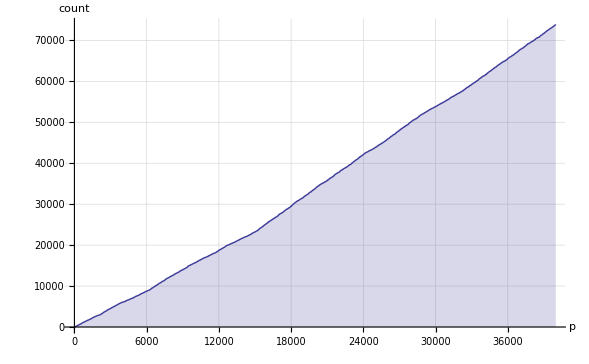

```mathematica
ListPlot[stepFunction , Joined->True,  Filling->Axis, GridLines->Automatic, AxesLabel->{"p","count"}]
```

```mathematica
InterpolatingPolynomial[Take[myValues,{100,110}], n]
```

800+(9+(1/2+(1/6+(-1/8+(1/40+(1/120+(-37/5040+(3/1120+(-17/25920+(439 (-10+n))/3628800) (-9+n)) (-8+n)) (-7+n)) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n)

```mathematica
FindGeneratingFunction[Take[myValues,{100,110}], n]
```

FindGeneratingFunction[{800,809,819,831,843,853,868,882,894,907,920},n]

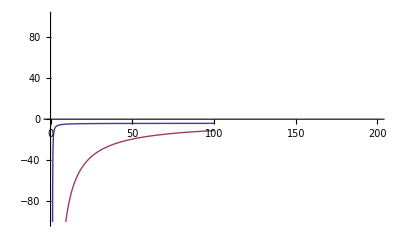

```mathematica
Plot[{3+(n (-8-7 (-2+n) n))/(-1+n)^3,800+(n (809+n (-2417-803 (-3+n) n)))/(-1+n)^4,800+(9+(1/2+(1/6+(-1/8+(1/40+(1/120+(-37/5040+(3/1120+(-17/25920+(439 (-10+n))/3628800) (-9+n)) (-8+n)) (-7+n)) (-6+n)) (-5+n)) (-4+n)) (-3+n)) (-2+n)) (-1+n)}, {n,1,100}, PlotRange->{{0,200},{-100,100}}]
```